Importing Survey Results

```mathematica
SetDirectory[NotebookDirectory[]];
Clear["Global`*"]
data=Table[elem->Import["20221101_JUB Survey on Renaming (Responses) - Anonymised.xlsx",elem,HeaderLines->1],{elem,Import["20221031_JUB Survey on Renaming (Responses) - Anonymised.xlsx","Elements",HeaderLines->1]}];
```

Data Preprocessing

```mathematica
status=(Values@data[[1]])[[1]][[All,2]];
field=(Values@data[[1]])[[1]][[All,3]];
renamingPlanheard=(Values@data[[1]])[[1]][[All,4]];
meetingAttended=(Values@data[[1]])[[1]][[All,5]];
nameRemain=(Values@data[[1]])[[1]][[All,6]];
feelAssosJUB=(Values@data[[1]])[[1]][[All,7]];
assosJUB=DeleteCases[(Values@data[[1]])[[1]][[All,8]],""];
assosCONS=DeleteCases[(Values@data[[1]])[[1]][[All,9]],""];
feelAssosCONS=(Values@data[[1]])[[1]][[All,10]];
wantToWork=(Values@data[[1]])[[1]][[All,11]];
alternativeName=(Values@data[[1]])[[1]][[All,12]];
ideas=DeleteCases[(Values@data[[1]])[[1]][[All,13]],""];
assosJUBText=StringJoin[Riffle[assosJUB,". "]];
assosCONSText=StringJoin[Riffle[assosCONS,". "]];
ideasText=StringJoin[Riffle[ideas,". "]];
```

Data Visualisations for Survey Results

Question 1 - What is your current status at the University?

```mathematica
pos1=Flatten@Position[StringContainsQ[status,{"Parents","Retired","(non-)","postdoc","foundation","adjunct","freelancer","exchange","/faculty"},IgnoreCase->True],True];
status2=ReplacePart[status,{Partition[pos1,1]->"Other Response Options"}];
chartdata=ReverseSort@Counts@status2;
chartstyle=Flatten@{Darker@Blue,Lighter@Blue,Orange,Darker@Green,Red,White,Purple};
PieChart[N[chartdata/Total@chartdata],ChartLegends->MapThread[ToString@#1<>" ("<>ToString@#2<>")"&,{Keys@chartdata,Values@chartdata}],ChartStyle->chartstyle,LabelingFunction->(Placed[Row[{NumberForm[100#,{3,1}],"%"}],"RadialCallout"]&),ImageSize->Medium]
```

-Graphics-

Question 2 - What is your field of study/research/work?

```mathematica
chartdata=ReverseSort@Counts@field;
chartstyle=Flatten@{Blue,Red,Orange,Darker@Green,Lighter@Blue,Purple,ConstantArray[White,20]};
PieChart[N[chartdata/Total@chartdata],ChartLegends->MapThread[ToString@#1<>" ("<>ToString@#2<>")"&,{Keys@chartdata,Values@chartdata}],ChartStyle->chartstyle,LabelingFunction->(Placed[Row[{NumberForm[100#,{3,1}],"%"}],"RadialCallout"]&)]
```

-Graphics-

Question 3 - Have you heard about the renaming plans of Jacobs University Bremen?

```mathematica
chartdata=ReverseSort@Counts@renamingPlanheard;
chartstyle={Blue,Red,Orange};
PieChart[N[chartdata/Total@chartdata],ChartLegends->MapThread[ToString@#1<>" ("<>ToString@#2<>")"&,{Keys@chartdata,Values@chartdata}],ChartStyle->chartstyle,LabelingFunction->(Placed[Row[{NumberForm[100#,{3,1}],"%"}],"RadialCallout"]&)]
```

-Graphics-

Question 4 - Have you attended the Town Hall meeting on September 22nd?

```mathematica
chartdata=ReverseSort@Counts@meetingAttended;
chartstyle={Red,Blue};
PieChart[N[chartdata/Total@chartdata],ChartLegends->MapThread[ToString@#1<>" ("<>ToString@#2<>")"&,{Keys@chartdata,Values@chartdata}],ChartStyle->chartstyle,LabelingFunction->(Placed[Row[{NumberForm[100#,{3,1}],"%"}],"RadialCallout"]&)]
```

-Graphics-

Question 5 - Do you want the current name of the University - Jacobs University Bremen - to remain?

```mathematica
chartdata=ReverseSort@Counts@nameRemain;
chartstyle={Blue,Orange,Red};
PieChart[N[chartdata/Total@chartdata],ChartLegends->MapThread[ToString@#1<>" ("<>ToString@#2<>")"&,{Keys@chartdata,Values@chartdata}],ChartStyle->chartstyle,LabelingFunction->(Placed[Row[{NumberForm[100#,{3,1}],"%"}],"RadialCallout"]&)]
```

-Graphics-

Question 6 - How strongly do you feel your association with “Jacobs University Bremen”?

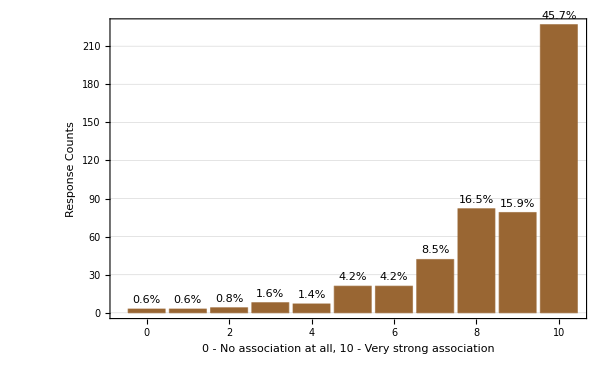

```mathematica
chartdata=KeySort@Counts@feelAssosJUB;
BarChart[chartdata,ChartStyle->Brown,GridLines->Automatic,ChartLabels->{IntegerPart@Keys@chartdata},LabelingFunction->(Placed[Row[{NumberForm[100(N[#/Total@chartdata]),{3,1}],"%"}],Above]&),Frame->True,FrameLabel->{"0 - No association at all, 10 - Very strong association","Response Counts"}]
```

Question 7 - What comes to your mind when you hear the name of the University - “Jacobs University Bremen”?

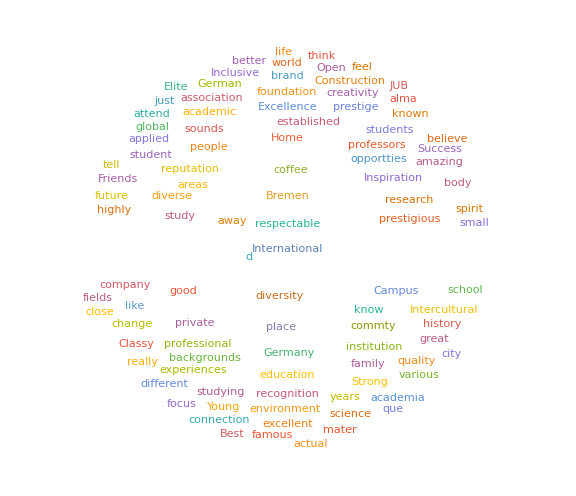

```mathematica
WordCloud[StringDelete[assosJUBText,{"university","University","UNIVERSITY","Uni","uni","Jacobs","JACOBS","jacobs","Constructor","constructor","name"}],ImageSize->Large]
```

Question 8 - What comes to your mind when you hear the name of the University - “Constructor University”?

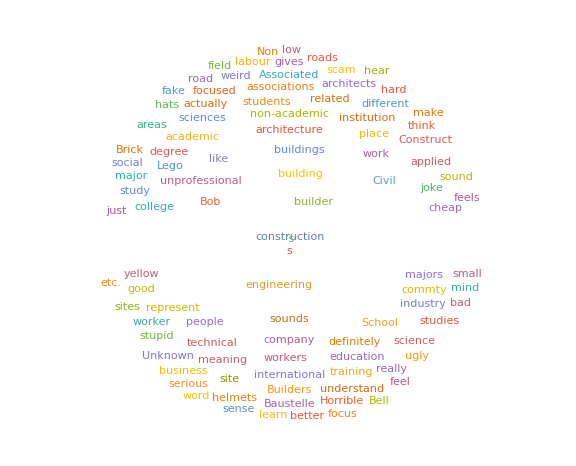

```mathematica
WordCloud[StringDelete[assosCONSText,{"university","University","UNIVERSITY","Uni","uni","Jacobs","JACOBS","jacobs","Constructor","constructor","name"}],ImageSize->Large]
```

Question 9 - How do you feel about renaming the University as “Constructor University”?

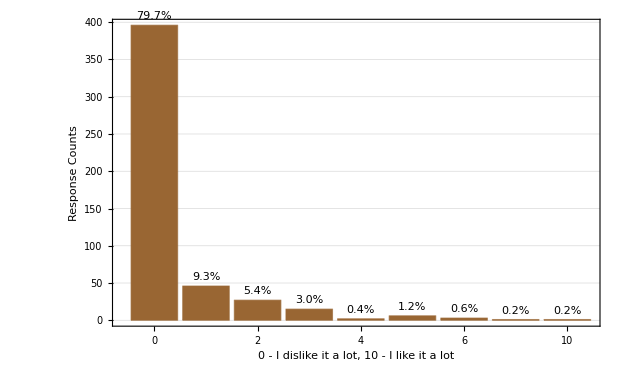

```mathematica
chartdata=KeySort@Counts@feelAssosCONS;
BarChart[chartdata,ChartStyle->Brown,GridLines->Automatic,ChartLabels->{IntegerPart@Keys@chartdata},LabelingFunction->(Placed[Row[{NumberForm[100(N[#/Total@chartdata]),{3,1}],"%"}],Above]&),Frame->True,FrameLabel->{"0 - I dislike it a lot, 10 - I like it a lot","Response Counts"}]
```

Question 10 - Do you want to study/work at the “Constructor University”?

```mathematica
chartdata=ReverseSort@Counts@wantToWork;
chartstyle={Red,Orange,Blue};
PieChart[N[chartdata/Total@chartdata],ChartLegends->MapThread[ToString@#1<>" ("<>ToString@#2<>")"&,{Keys@chartdata,Values@chartdata}],ChartStyle->chartstyle,LabelingFunction->(Placed[Row[{NumberForm[100#,{3,1}],"%"}],"RadialCallout"]&)]
```

-Graphics-

Question 11 - In case the current name is not kept, which name do you think Jacobs University Bremen should have in the future?

```mathematica
pos1=Flatten@Position[StringCases[alternativeName,{"international", "university", "bremen"},IgnoreCase->True],_?(Length@#==3&)];
pos1a=Flatten@Position[StringContainsQ[alternativeName,{"IUB"},IgnoreCase->True],True];
pos2=Flatten@Position[StringContainsQ[alternativeName,{"bremen institute of technology and science"},IgnoreCase->True],True];
pos2a=Flatten@Position[StringCases[alternativeName,{"bremen", "institute", "of", "technology", "and", "science"},IgnoreCase->True],_?(Length@#==6&)];
pos3=Flatten@Position[StringContainsQ[alternativeName,{"BIT - Bremen Institute of Techology","bremen institute of technology"},IgnoreCase->True],True];
pos4=Flatten@Position[StringContainsQ[alternativeName,{"I think the most healty thing","So a name should embody the spirit of diversity that jacobs champions","any name which is not clearly associated with a potential","society/politics etc.","none of the above represents what Jacobs stands for","Different unique name","Some artificial name that vaguely sounds like Latin"},IgnoreCase->True],True];
pos5=Flatten@Position[StringContainsQ[alternativeName,{"Polytechnische Hochschule Bremen","Charles Babbage University","Bell University Bremen","Jacobs International University","Jacobs University is in itself a best name this university can have","Technique University Bremen","Bremen Technological University","Bremen University of Science and Technology","Slay University","Paradigm University","options besides Constructor","Wesser River University","Lucid Dream University","For Whom The Bell Tolls","except Constructor Univeristy","Schaffhausen Institute of Technology Bremen","?","Bell University","Bell International University","Innovator","Constructive","International Global Challenges University (IGCU)","None of Them"},IgnoreCase->True],True];
alternativeName2=ReplacePart[alternativeName,{Partition[Union[pos1,pos1a],1]->"International University Bremen",Partition[Union[pos2a,pos2],1]->"Bremen Institute of Technology and Science",Partition[Complement[pos3,pos2a],1]->"Bremen Institute of Technology",Partition[pos4,1]->"A Unique Name", Partition[pos5,1]->"Other Response Options"}];
chartdata=ReverseSort@Counts@alternativeName2;
chartstyle=Flatten@{Red,Darker@Green,Orange,White,Lighter@Blue,Purple,Yellow,Blue};
PieChart[N[chartdata/Total@chartdata],ChartLegends->MapThread[ToString@#1<>" ("<>ToString@#2<>")"&,{Keys@chartdata,Values@chartdata}],ChartStyle->chartstyle,LabelingFunction->(Placed[Row[{NumberForm[100#,{3,1}],"%"}],"RadialCallout"]&)]
```

-Graphics-

Question 12 - Please share your ideas and suggestions with the GSA and BIGSSS Fellow Representatives

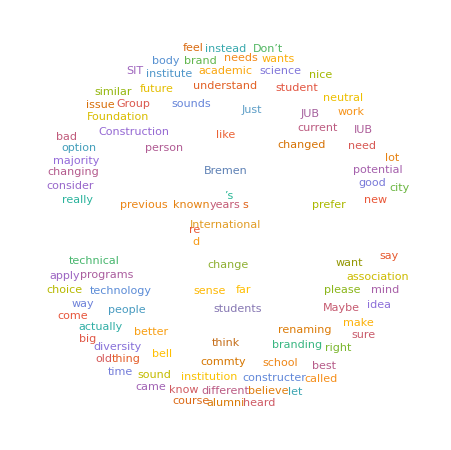

```mathematica
WordCloud@StringDelete[ideasText,{"university","University","UNIVERSITY","Uni","uni","Jacobs","JACOBS","jacobs","Constructor","constructor","name"}]
```

Text Analysis with Semantic Interpretation

Analysis for  the data collected from Question 12

Extracting notable text contents and displaying the frequency of content strings found in the text with the respective content types and interpretation

```mathematica
contentsOfAssociationsForIdeas=TextContents[ideasText,VerifyInterpretation->True];
{countsForIdeasAssociationsContentString=ReverseSort@CountsBy[contentsOfAssociationsForIdeas,#String&],countsForIdeasAssociationsContentType=ReverseSort@CountsBy[contentsOfAssociationsForIdeas,#Type&],countsForIdeasAssociationsContentInterpre=ReverseSort@CountsBy[contentsOfAssociationsForIdeas,#Interpretation&]}
entitylist=Table[(Keys@countsForIdeasAssociationsContentType)[[i]],{i,Length@countsForIdeasAssociationsContentType}]
```

{,,}

{University,Surname,Person,HistoricalCountry,Country,GivenName,Language,City,Quantity,Date,Financial,Company,PersonTitle,AdministrativeDivision,GeographicRegion}

For Category: University, finding notable potential properties, interpreting them as entities and visualising them in a Word Cloud

```mathematica
(* 1 -> University, 5 -> Country, 8 -> City *)
x=1;
Print["Strings for Ideas: \n",stringsOfAssociationsForIdeas=Normal[Select[contentsOfAssociationsForIdeas,#Type===entitylist[[x]]&][[All,"String"]]]]
Print["Interpretations for Idea Strings: \n",interpretationsOfAssociationsForIdeas=Normal[Select[contentsOfAssociationsForIdeas,#Type===entitylist[[x]]&][[All,"Interpretation"]]]]
resultArray=Table[EntityValue[interpretationsOfAssociationsForIdeas,EntityProperties[entitylist[[x]]][[i]]],{i,Length@EntityProperties[entitylist[[x]]]}];
WordCloud@Counts@DeleteMissing@Flatten@resultArray
```

Strings for Ideas: 
{university,IUB,International University Bremen,International University Bremen,Univerity,University,University,Jacobs University,Stanford,Harvard,University,Jacobs University,IUB,International University Bremen,IUB,IUB,International University Bremen,University,International University Bremen,International University Bremen,university,Jacobs University,Jacobs University,Jacobs University,University,IUB,International University Bremen,Global University,IUB,Jacobs University,Jacobs University,International University Bremen,International University Bremen,Jacobs University,International University Bremen,International university,science and technology,International University Bremen,university,International University Bremen,International University Bremen,jacobs university,University,University,Jacobs University,University,University,UNIVERSITY,Jacobs University,International University Bremen,international university bremen,Jacobs University,International University,International University Bremen,Jacobs University Bremen,IUB,Jacobs University Bremen,International University Bremen,International University Bremen,Jacobs University,International University Bremen,International University Bremen,City,Jacobs University,IUB,IUB,University,International University Bremen,International University Bremen}

Interpretations for Idea Strings: 
{University College,Indiana University Bloomington,Jacobs University Bremen,Jacobs University Bremen,University College,University College,University College,Jacobs University Bremen,Stanford University,Harvard University,University College,Jacobs University Bremen,Indiana University Bloomington,Jacobs University Bremen,Indiana University Bloomington,Indiana University Bloomington,Jacobs University Bremen,University College,Jacobs University Bremen,Jacobs University Bremen,University College,Jacobs University Bremen,Jacobs University Bremen,Jacobs University Bremen,University College,Indiana University Bloomington,Jacobs University Bremen,Global University,Indiana University Bloomington,Jacobs University Bremen,Jacobs University Bremen,Jacobs University Bremen,Jacobs University Bremen,Jacobs University Bremen,Jacobs University Bremen,Universidade Internacional,University of Science and Technology,Jacobs University Bremen,University College,Jacobs University Bremen,Jacobs University Bremen,Jacobs University Bremen,University College,University College,Jacobs University Bremen,University College,University College,University College,Jacobs University Bremen,Jacobs University Bremen,Jacobs University Bremen,Jacobs University Bremen,Universidade Internacional,Jacobs University Bremen,Jacobs University Bremen,Indiana University Bloomington,Jacobs University Bremen,Jacobs University Bremen,Jacobs University Bremen,Jacobs University Bremen,Jacobs University Bremen,Jacobs University Bremen,City College,Jacobs University Bremen,Indiana University Bloomington,Indiana University Bloomington,University College,Jacobs University Bremen,Jacobs University Bremen}

-Graphics-

For Category: Country, finding notable potential properties, interpreting them as entities and visualising them in a Word Cloud

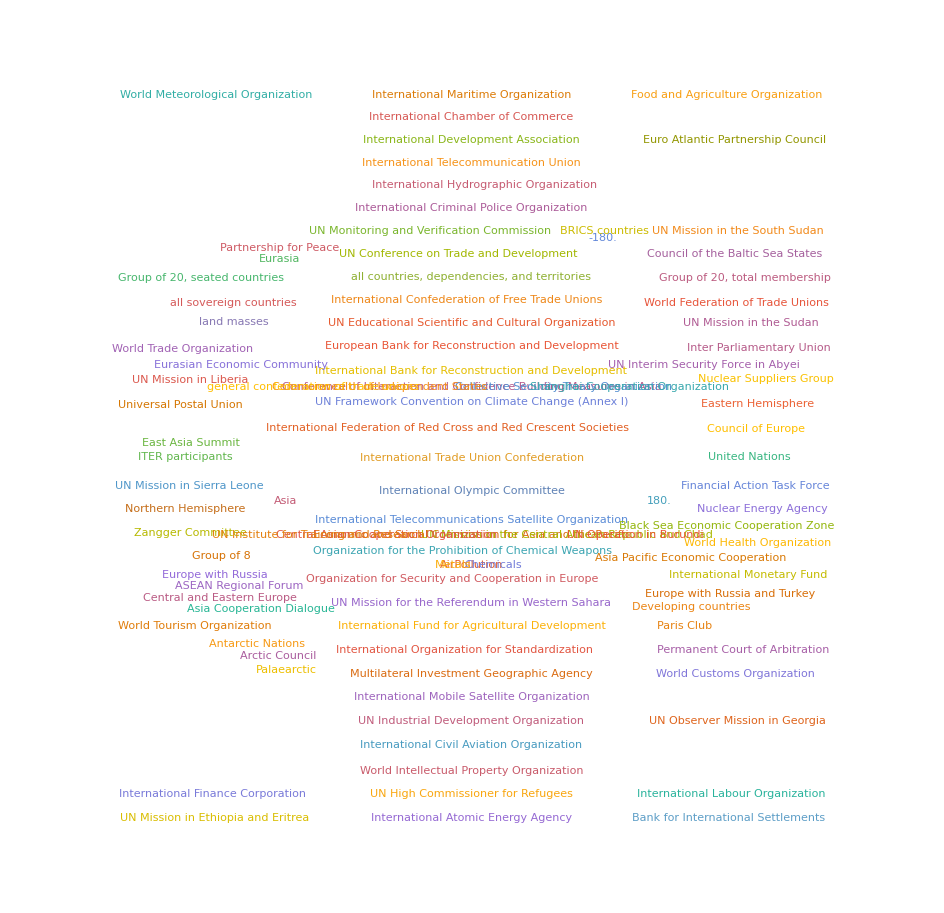

```mathematica
(* 1 -> University, 5 -> Country, 8 -> City *)
x=5;
Print["Strings for Ideas: \n",stringsOfAssociationsForIdeas=Normal[Select[contentsOfAssociationsForIdeas,#Type===entitylist[[x]]&][[All,"String"]]]]
Print["Interpretations for Idea Strings: \n",interpretationsOfAssociationsForIdeas=Normal[Select[contentsOfAssociationsForIdeas,#Type===entitylist[[x]]&][[All,"Interpretation"]]]]
resultArray=Table[EntityValue[interpretationsOfAssociationsForIdeas,EntityProperties[entitylist[[x]]][[i]]],{i,Length@EntityProperties[entitylist[[x]]]}];
WordCloud@Counts@DeleteMissing@Flatten@resultArray
```

For Category: City, finding notable potential properties, interpreting them as entities and visualising them in a Word Cloud

Strings for Ideas: 
{Schaffhausen,Bremen,Bremen,bremen,Bremen}

Interpretations for Idea Strings: 
{Schaffhausen,Bremen,Bremen,Bremen,Bremen}

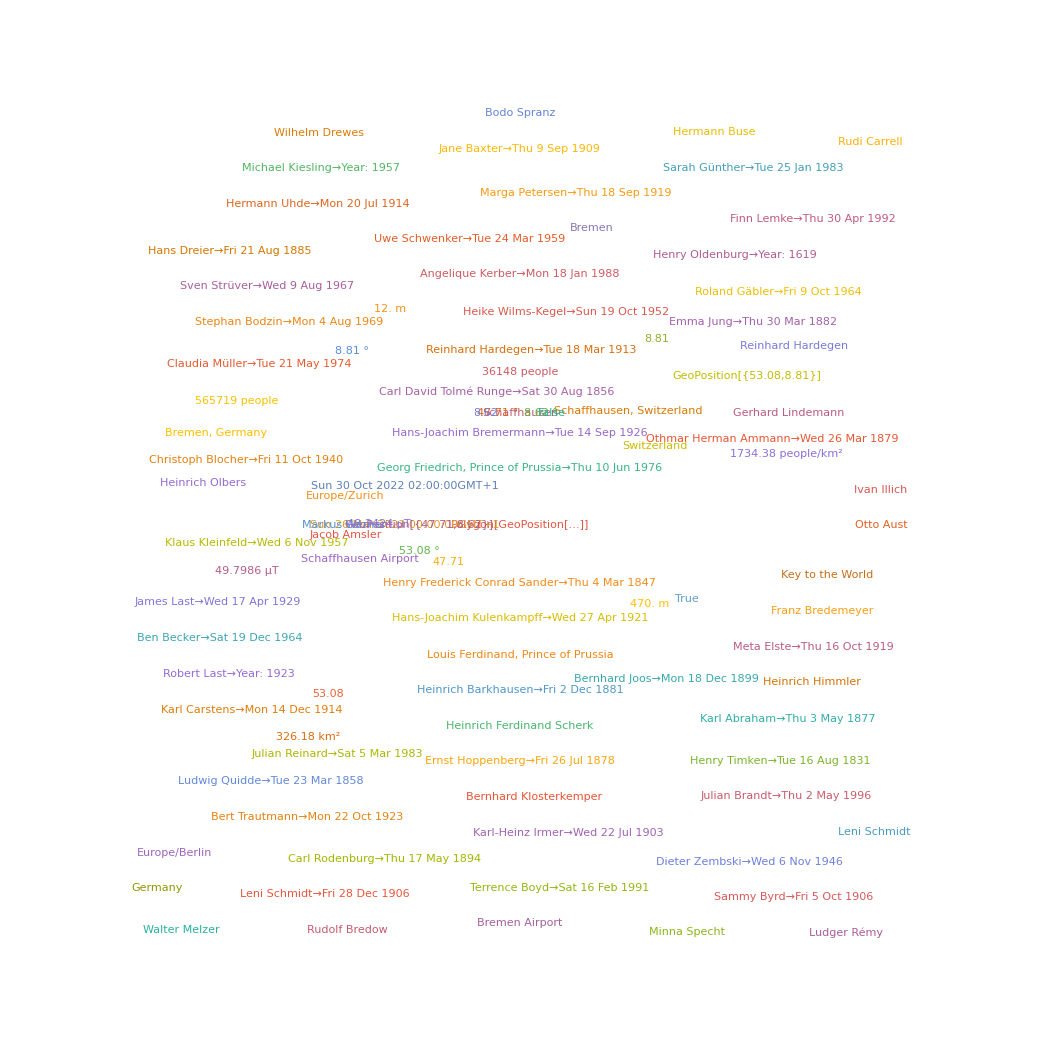

```mathematica
(* 1 -> University, 5 -> Country, 8 -> City *)
x=8;
Print["Strings for Ideas: \n",stringsOfAssociationsForIdeas=Normal[Select[contentsOfAssociationsForIdeas,#Type===entitylist[[x]]&][[All,"String"]]]]
Print["Interpretations for Idea Strings: \n",interpretationsOfAssociationsForIdeas=Normal[Select[contentsOfAssociationsForIdeas,#Type===entitylist[[x]]&][[All,"Interpretation"]]]]
resultArray=Table[EntityValue[interpretationsOfAssociationsForIdeas,EntityProperties[entitylist[[x]]][[i]]],{i,Length@EntityProperties[entitylist[[x]]]}];
WordCloud@Counts@DeleteMissing@Flatten@resultArray
```

Analysis for  the data collected from Question 8

Extracting notable text contents and displaying the frequency of content strings found in the text with the respective content types and interpretation

```mathematica
contentsOfAssociationsForIdeas=TextContents[assosCONSText,VerifyInterpretation->True];
{countsForIdeasAssociationsContentString=ReverseSort@CountsBy[contentsOfAssociationsForIdeas,#String&],countsForIdeasAssociationsContentType=ReverseSort@CountsBy[contentsOfAssociationsForIdeas,#Type&],countsForIdeasAssociationsContentInterpre=ReverseSort@CountsBy[contentsOfAssociationsForIdeas,#Interpretation&]}
entitylist=Table[(Keys@countsForIdeasAssociationsContentType)[[i]],{i,Length@countsForIdeasAssociationsContentType}]
```

{,,}

{GivenName,University,Color,Surname,Person,HistoricalCountry,Country,Quantity,Movie,Neighborhood,Language,PersonTitle,ProgrammingLanguage,Species,Food,Financial,Company}

For Category: Country, finding notable potential properties, interpreting them as entities and visualising them in a Word Cloud

Strings for Ideas: 
{Filipinos,China,Germany}

Interpretations for Idea Strings: 
{Philippines,China,Germany}

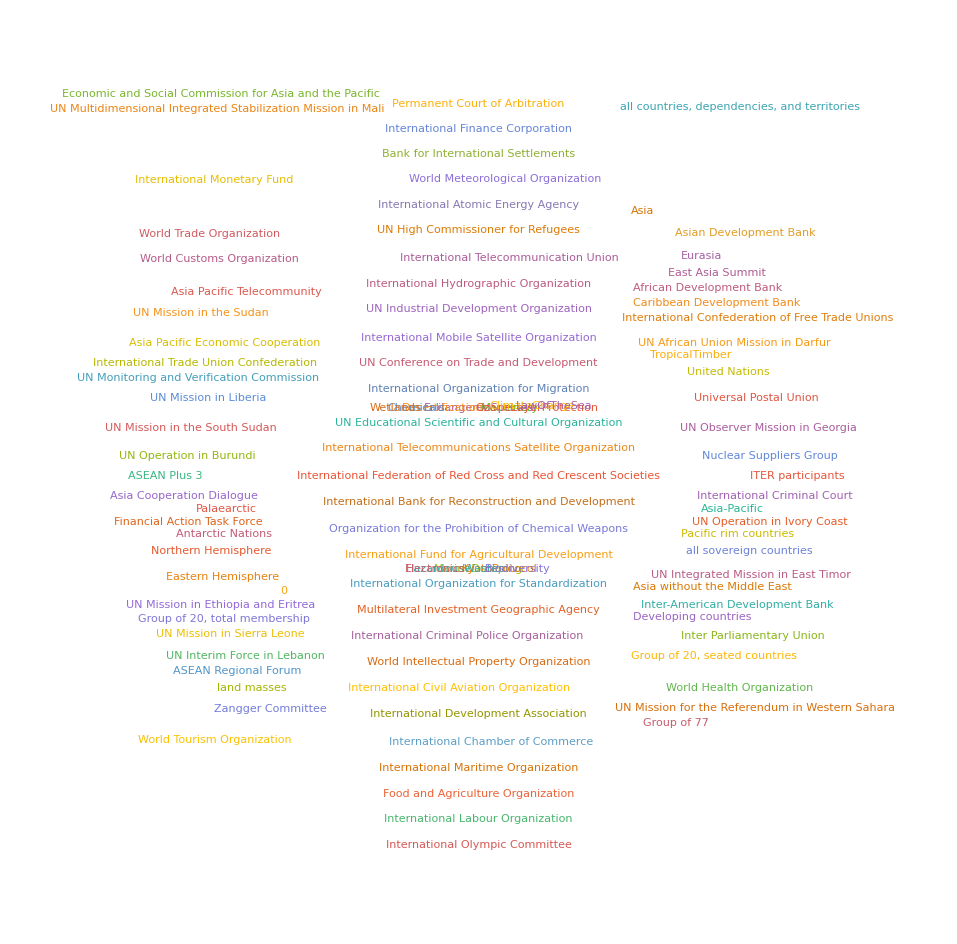

```mathematica
(* 7 -> Country *)
x=7;
Print["Strings for Ideas: \n",stringsOfAssociationsForIdeas=Normal[Select[contentsOfAssociationsForIdeas,#Type===entitylist[[x]]&][[All,"String"]]]]
Print["Interpretations for Idea Strings: \n",interpretationsOfAssociationsForIdeas=Normal[Select[contentsOfAssociationsForIdeas,#Type===entitylist[[x]]&][[All,"Interpretation"]]]]
resultArray=Table[EntityValue[interpretationsOfAssociationsForIdeas,EntityProperties[entitylist[[x]]][[i]]],{i,Length@EntityProperties[entitylist[[x]]]}];
WordCloud@Counts@DeleteMissing@Flatten@resultArray
```